```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3+c04 x^4, 0≤x≤1/2}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3+c14(x-1)^4, 1/2<x≤3/2}, {c21(x-2)+c22(x-2)^2+c23(x-2)^3+c24(x-2)^4, 3/2<x≤5/2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Continuity*)
C1l=Simplify[h[x],0≤x≤1/2]/.x->1/2
C1r=Simplify[h[x],1/2<x≤3/2]/.x->1/2
C2l=Simplify[h[x],1/2<x≤3/2]/.x->3/2
C2r=Simplify[h[x],3/2<x≤5/2]/.x->3/2
C3l=Simplify[h[x],3/2<x≤5/2]/.x->5/2
```

1+c01/2+c02/4+c03/8+c04/16

1/2 (-c11+1/2 (c12+1/2 (-c13+c14/2)))

1/2 (c11+1/2 (c12+1/2 (c13+c14/2)))

1/2 (-c21+1/2 (c22+1/2 (-c23+c24/2)))

1/2 (c21+1/2 (c22+1/2 (c23+c24/2)))

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[∑_(i=-6)^6 f[x-i],x>0&&x<1/2],x]
T1=CoefficientList[FullSimplify[∑_(i=-6)^6 i f[x-i],x>0&&x<1/2],x]
```

{1,c01,c02+2 (c12+c22),c03,c04+2 (c14+c24)}

{0,-2 c11-4 c21,0,-2 (c13+2 c23)}

```mathematica
GenSols=Solve[{
	C1l==C1r,
	C2l==C2r,
	C3l==0,
	T0[[2]]==0,
	T0[[3]]==0,
	T0[[4]]==0,
	T0[[5]]==0,
	T1[[2]]==1,
	T1[[4]]==0
	},
	{c01,c02,c03,c04,c11,c12,c13,c14,c21,c22,c23,c24}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c01→0,c03→0,c13→-6-2 c02-c04/2-4 c11,c14→4-4 c12,c21→-1/4-c11/2,c22→-c02/2-c12,c23→3+c02+c04/4+2 c11,c24→-4-c04/2+4 c12}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-5)^6 ∑_(j=-5)^6 W1[i-j]f[x-i,y-j]/.GenSol;
SumF1=SumF1/.φ->1/2;
```

```mathematica
{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}=Parallelize[{
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>0-1/2&&x<1-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>1-1/2&&y<2-1/2],
	Simplify[SumF1,x>-1-1/2&&x<0-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>2-1/2&&y<3-1/2],
	Simplify[SumF1,x>-2-1/2&&x<-1-1/2&&y>3-1/2&&y<4-1/2]
}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}=Parallelize[{
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>0-1/2&&y<1-1/2],
	Simplify[SumF1,x>1-1/2&&x<2-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-1-1/2&&y<0-1/2],
	Simplify[SumF1,x>2-1/2&&x<3-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-2-1/2&&y<-1-1/2],
	Simplify[SumF1,x>3-1/2&&x<4-1/2&&y>-3-1/2&&y<-2-1/2]
}];
```

```mathematica
TableForm[{SumF1a1,SumF1a2,SumF1a3,SumF1a4,SumF1a5,SumF1a6}]
TableForm[{SumF1b1,SumF1b2,SumF1b3,SumF1b4,SumF1b5,SumF1b6}]
```

1/64 (-(12+4 c02+c04+8 c11) x^3 (-12-2 (1+13 c11) y-2 (9 c02+7 c12) y^2+13 (12+4 c02+c04+8 c11) y^3-2 (28+9 c04-28 c12) y^4)-4 (-2+(4-6 c11) y+2 (3 c02+c12) y^2+3 (12+4 c02+c04+8 c11) y^3+(8+6 c04-8 c12) y^4)-2 x^2 (1+2 y) (18 c02^2 y^2+c12 (4-(1+14 c11) y+(2+28 c11+40 c12) y^2+(80+7 c04-80 c12) y^3)+c02 (12-2 (10+9 c11) y+4 (10+9 c11+7 c12) y^2+(28+9 c04-28 c12) y^3))-2 x^4 (1+2 y) (9 c04^2 y^3+2 c04 (6-(10+9 c11) y+(20+9 c02+18 c11+7 c12) y^2-28 (-1+c12) y^3)+4 (-1+c12) (-4+y+14 c11 y-2 (1+7 c02+14 c11+20 c12) y^2+80 (-1+c12) y^3))+x (16-3 y+2 (4 c02+7 c12) y^2+2 (12+4 c02+c04) y^3+8 (7+c04-7 c12) y^4+52 c11^2 y (-1+4 y^2)+2 c11 (-12-4 y-2 (9 c02+7 c12) y^2+(164+52 c02+13 c04) y^3-2 (28+9 c04-28 c12) y^4)))
1/32 (-7 x (1+2 x) (-1+2 (1+c02+2 c12) x+(8+c04-8 c12) x^2+c11 (-2+4 x)) (1+c02 (-1+y)^2+c04 (-1+y)^4)+2 x (c11 (-2+8 x^2)+x (x (12+4 c02+c04+8 x)+c12 (2-8 x^2))) (1+c02 (-1+y)^2+c04 (-1+y)^4)+4 (1+c02 x^2+c04 x^4) (c11+c12 (-1+y)-1/2 (12+4 c02+c04+8 c11) (-1+y)^2-4 (-1+c12) (-1+y)^3) (-1+y)-8 x (1+2 x) (-1+2 (1+c02+2 c12) x+(8+c04-8 c12) x^2+c11 (-2+4 x)) (c11+c12 (-1+y)-1/2 (12+4 c02+c04+8 c11) (-1+y)^2-4 (-1+c12) (-1+y)^3) (-1+y)+14 x (c11 (-2+8 x^2)+x (x (12+4 c02+c04+8 x)+c12 (2-8 x^2))) (c11+c12 (-1+y)-1/2 (12+4 c02+c04+8 c11) (-1+y)^2-4 (-1+c12) (-1+y)^3) (-1+y)-x (1+2 x) (-1+2 (1+c02+2 c12) x+(8+c04-8 c12) x^2+c11 (-2+4 x)) (1-y) (c11+c12-1/2 (12+4 c02+c04+8 c11) (-1+y)^2+4 (-1+c12) (-1+y)^3-c12 y)-x (c11+c12 x-1/2 (12+4 c02+c04+8 c11) x^2-4 (-1+c12) x^3) (-1+y) (-3+2 y) (9+2 c11-4 c12-2 c02 (-1+y)+c04 (-1+y)^2-18 y-4 c11 y+12 c12 y+8 y^2-8 c12 y^2)-7 (1+c02 x^2+c04 x^4) (-1+y) (-3+2 y) (9+2 c11-4 c12-2 c02 (-1+y)+c04 (-1+y)^2-18 y-4 c11 y+12 c12 y+8 y^2-8 c12 y^2)+2 x (1+2 x) (-1+2 (1+c02+2 c12) x+(8+c04-8 c12) x^2+c11 (-2+4 x)) (-1+y) (-3+2 y) (9+2 c11-4 c12-2 c02 (-1+y)+c04 (-1+y)^2-18 y-4 c11 y+12 c12 y+8 y^2-8 c12 y^2)-4 x (c11 (-2+8 x^2)+x (x (12+4 c02+c04+8 x)+c12 (2-8 x^2))) (-1+y) (-3+2 y) (9+2 c11-4 c12-2 c02 (-1+y)+c04 (-1+y)^2-18 y-4 c11 y+12 c12 y+8 y^2-8 c12 y^2))
1/32 (-(1+x) (3+2 x) (9+2 c11-4 c12+18 x+4 c11 x-12 c12 x+8 x^2-8 c12 x^2+2 c02 (1+x)+c04 (1+x)^2) (1+c02 (-1+y)^2+c04 (-1+y)^4)-7 (1+x) (3+2 x) (9+2 c11-4 c12+18 x+4 c11 x-12 c12 x+8 x^2-8 c12 x^2+2 c02 (1+x)+c04 (1+x)^2) (c11+c12 (-1+y)-1/2 (12+4 c02+c04+8 c11) (-1+y)^2-4 (-1+c12) (-1+y)^3) (-1+y)+4 (-1-x) (c11-c12 (1+x)-1/2 (12+4 c02+c04+8 c11) (1+x)^2+4 (-1+c12) (1+x)^3) (c11+c12 (-1+y)-1/2 (12+4 c02+c04+8 c11) (-1+y)^2-4 (-1+c12) (-1+y)^3) (-1+y)+2 (1+x) (3+2 x) (9+2 c11-4 c12+18 x+4 c11 x-12 c12 x+8 x^2-8 c12 x^2+2 c02 (1+x)+c04 (1+x)^2) (-1+y) (-3+2 y) (9+2 c11-4 c12-2 c02 (-1+y)+c04 (-1+y)^2-18 y-4 c11 y+12 c12 y+8 y^2-8 c12 y^2)-7 (-1-x) (c11-c12 (1+x)-1/2 (12+4 c02+c04+8 c11) (1+x)^2+4 (-1+c12) (1+x)^3) (-1+y) (-3+2 y) (9+2 c11-4 c12-2 c02 (-1+y)+c04 (-1+y)^2-18 y-4 c11 y+12 c12 y+8 y^2-8 c12 y^2)-(1+c02 (1+x)^2+c04 (1+x)^4) (-1+y) (-3+2 y) (9+2 c11-4 c12-2 c02 (-1+y)+c04 (-1+y)^2-18 y-4 c11 y+12 c12 y+8 y^2-8 c12 y^2))
1/128 (-7 (1+x) (3+2 x) (9+2 c11-4 c12+18 x+4 c11 x-12 c12 x+8 x^2-8 c12 x^2+2 c02 (1+x)+c04 (1+x)^2) (-1-2 c11-2 (c02+2 c12) (-2+y)+(12+4 c02+c04+8 c11) (-2+y)^2-2 (8+c04-8 c12) (-2+y)^3)+4 (-1-x) (c11-c12 (1+x)-1/2 (12+4 c02+c04+8 c11) (1+x)^2+4 (-1+c12) (1+x)^3) (-1-2 c11-2 (c02+2 c12) (-2+y)+(12+4 c02+c04+8 c11) (-2+y)^2-2 (8+c04-8 c12) (-2+y)^3)-4 (1+x) (3+2 x) (9+2 c11-4 c12+18 x+4 c11 x-12 c12 x+8 x^2-8 c12 x^2+2 c02 (1+x)+c04 (1+x)^2) (c11+c12 (-2+y)-1/2 (12+4 c02+c04+8 c11) (-2+y)^2-4 (-1+c12) (-2+y)^3)) (-2+y)
-1/128 (2+x) (5+2 x) (35+6 c11-24 c12+34 x+4 c11 x-28 c12 x+8 x^2-8 c12 x^2+2 c02 (2+x)+c04 (2+x)^2) (-1-2 c11-2 (c02+2 c12) (-2+y)+(12+4 c02+c04+8 c11) (-2+y)^2-2 (8+c04-8 c12) (-2+y)^3) (-2+y)
0

1/128 (128 (1+c02 (-1+x)^2+c04 (-1+x)^4) y (c11+c12 y-1/2 (12+4 c02+c04+8 c11) y^2-4 (-1+c12) y^3)+112 (c11+c12 (-1+x)-1/2 (12+4 c02+c04+8 c11) (-1+x)^2-4 (-1+c12) (-1+x)^3) (-1+x) y (c11+c12 y-1/2 (12+4 c02+c04+8 c11) y^2-4 (-1+c12) y^3)+128 (1-x) (c11+c12-1/2 (12+4 c02+c04+8 c11) (-1+x)^2+4 (-1+c12) (-1+x)^3-c12 x) y (c11+c12 y-1/2 (12+4 c02+c04+8 c11) y^2-4 (-1+c12) y^3)-4 (-1+x) (-3+2 x) (9+2 c11-4 c12-2 c02 (-1+x)+c04 (-1+x)^2-18 x-4 c11 x+12 c12 x+8 x^2-8 c12 x^2) y (c11+c12 y-1/2 (12+4 c02+c04+8 c11) y^2-4 (-1+c12) y^3)-32 (-1+x) (-1+2 x) (5-6 c11-12 c12+2 c02 (-1+x)+c04 (-1+x)^2-14 x+4 c11 x+20 c12 x+8 x^2-8 c12 x^2) y (c11+c12 y-1/2 (12+4 c02+c04+8 c11) y^2-4 (-1+c12) y^3)+112 (1+c02 (-1+x)^2+c04 (-1+x)^4) (1+c02 y^2+c04 y^4)+16 (c11+c12 (-1+x)-1/2 (12+4 c02+c04+8 c11) (-1+x)^2-4 (-1+c12) (-1+x)^3) (-1+x) (1+c02 y^2+c04 y^4)+128 (1-x) (c11+c12-1/2 (12+4 c02+c04+8 c11) (-1+x)^2+4 (-1+c12) (-1+x)^3-c12 x) (1+c02 y^2+c04 y^4)-32 (-1+x) (-1+2 x) (5-6 c11-12 c12+2 c02 (-1+x)+c04 (-1+x)^2-14 x+4 c11 x+20 c12 x+8 x^2-8 c12 x^2) (1+c02 y^2+c04 y^4)-4 (1-x) (c11+c12-1/2 (12+4 c02+c04+8 c11) (-1+x)^2+4 (-1+c12) (-1+x)^3-c12 x) y (1+2 y) (-1+2 (1+c02+2 c12) y+(8+c04-8 c12) y^2+c11 (-2+4 y))+7 (-1+x) (-1+2 x) (5-6 c11-12 c12+2 c02 (-1+x)+c04 (-1+x)^2-14 x+4 c11 x+20 c12 x+8 x^2-8 c12 x^2) y (1+2 y) (-1+2 (1+c02+2 c12) y+(8+c04-8 c12) y^2+c11 (-2+4 y))+32 (1+c02 (-1+x)^2+c04 (-1+x)^4) y (-1+2 y) (1+2 (1+c02+2 c12) y-(8+c04-8 c12) y^2+c11 (2+4 y))+32 (c11+c12 (-1+x)-1/2 (12+4 c02+c04+8 c11) (-1+x)^2-4 (-1+c12) (-1+x)^3) (-1+x) y (-1+2 y) (1+2 (1+c02+2 c12) y-(8+c04-8 c12) y^2+c11 (2+4 y))+32 (1-x) (c11+c12-1/2 (12+4 c02+c04+8 c11) (-1+x)^2+4 (-1+c12) (-1+x)^3-c12 x) y (-1+2 y) (1+2 (1+c02+2 c12) y-(8+c04-8 c12) y^2+c11 (2+4 y))-7 (-1+x) (-3+2 x) (9+2 c11-4 c12-2 c02 (-1+x)+c04 (-1+x)^2-18 x-4 c11 x+12 c12 x+8 x^2-8 c12 x^2) y (-1+2 y) (1+2 (1+c02+2 c12) y-(8+c04-8 c12) y^2+c11 (2+4 y))-8 (-1+x) (-1+2 x) (5-6 c11-12 c12+2 c02 (-1+x)+c04 (-1+x)^2-14 x+4 c11 x+20 c12 x+8 x^2-8 c12 x^2) y (-1+2 y) (1+2 (1+c02+2 c12) y-(8+c04-8 c12) y^2+c11 (2+4 y))+8 (1+c02 (-1+x)^2+c04 (-1+x)^4) y (c11 (-2+8 y^2)+y (y (12+4 c02+c04+8 y)+c12 (2-8 y^2)))+56 (1-x) (c11+c12-1/2 (12+4 c02+c04+8 c11) (-1+x)^2+4 (-1+c12) (-1+x)^3-c12 x) y (c11 (-2+8 y^2)+y (y (12+4 c02+c04+8 y)+c12 (2-8 y^2)))-16 (-1+x) (-1+2 x) (5-6 c11-12 c12+2 c02 (-1+x)+c04 (-1+x)^2-14 x+4 c11 x+20 c12 x+8 x^2-8 c12 x^2) y (c11 (-2+8 y^2)+y (y (12+4 c02+c04+8 y)+c12 (2-8 y^2))))
1/64 (8 c02^2 (-1+x)^2 (1+y)^2 (13+8 x y)+4 c04^2 (-1+x)^3 (1+y)^3 (-17-14 y+2 x (7+5 y))+2 c02 (290-695 x+48 c11 x+733 x^2-96 c11 x^2-414 x^3+48 c11 x^3+120 x^4+695 y-48 c11 y-1424 x y+352 c11 x y+1259 x^2 y-544 c11 x^2 y-698 x^3 y+240 c11 x^3 y+256 x^4 y+733 y^2-96 c11 y^2-1259 x y^2+544 c11 x y^2+672 x^2 y^2-768 c11 x^2 y^2-224 x^3 y^2+320 c11 x^3 y^2+152 x^4 y^2+414 y^3-48 c11 y^3-698 x y^3+240 c11 x y^3+224 x^2 y^3-320 c11 x^2 y^3+64 x^3 y^3+128 c11 x^3 y^3+16 x^4 y^3+120 y^4-256 x y^4+152 x^2 y^4-16 x^3 y^4+4 c04 (-1+x)^2 (1+y)^2 (26+32 y+13 y^2+x^2 (13+8 y)-4 x (8+7 y+2 y^2))-4 c12 (-1+x)^2 (1+y)^2 (45+63 y+30 y^2+x^2 (30+4 y)-x (63+16 y+4 y^2)))+c04 (778-2876 x+4161 x^2-2663 x^3+638 x^4+2876 y-10526 x y+15075 x^2 y-9541 x^3 y+2258 x^4 y+4161 y^2-15075 x y^2+21312 x^2 y^2-13296 x^3 y^2+3096 x^4 y^2+2663 y^3-9541 x y^3+13296 x^2 y^3-8160 x^3 y^3+1864 x^4 y^3+638 y^4-2258 x y^4+3096 x^2 y^4-1864 x^3 y^4+416 x^4 y^4-2 c12 (-1+x)^2 (1+y)^2 (3 (54+125 y+62 y^2)+2 x^2 (93+210 y+104 y^2)-x (375+848 y+420 y^2))+8 c11 (-1+x) (1+y) (4 x^3 (3+8 y+4 y^2)-3 (6+18 y+15 y^2+4 y^3)+2 x (27+80 y+64 y^2+16 y^3)-x^2 (45+128 y+88 y^2+16 y^3)))+2 (284-703 x+1398 x^2-1130 x^3+332 x^4+703 y-1490 x y+3378 x^2 y-2942 x^3 y+908 x^4 y+1398 y^2-3378 x y^2+6048 x^2 y^2-4608 x^3 y^2+1296 x^4 y^2+1130 y^3-2942 x y^3+4608 x^2 y^3-3168 x^3 y^3+816 x^4 y^3+332 y^4-908 x y^4+1296 x^2 y^4-816 x^3 y^4+192 x^4 y^4+12 c12^2 (-1+x)^2 (3-8 x+4 x^2) (1+y)^2 (3+8 y+4 y^2)+8 c11^2 (-3+11 x-12 x^2+4 x^3) (3+11 y+12 y^2+4 y^3)-2 c11 (99+354 y+342 y^2+90 y^3-12 y^4-4 x^4 (3+11 y+12 y^2+4 y^3)+c12 (-3+11 x-12 x^2+4 x^3) (-2+x-y) (3+11 y+12 y^2+4 y^3)-6 x^2 (-57-203 y-192 y^2-48 y^3+8 y^4)+2 x^3 (-45-159 y-144 y^2-32 y^3+8 y^4)+x (-354-1265 y-1218 y^2-318 y^3+44 y^4))-c12 (498+1843 y+2881 y^2+1940 y^3+476 y^4+4 x^4 (119+395 y+600 y^2+396 y^3+96 y^4)-4 x^3 (485+1622 y+2469 y^2+1632 y^3+396 y^4)-x (1843+6356 y+9757 y^2+6488 y^3+1580 y^4)+x^2 (2881+9757 y+14904 y^2+9876 y^3+2400 y^4))))
1/64 (-8 c04^2 (-2+x)^3 (1+y)^3 (2+(-1+x) y)-8 c02^2 (-2+x)^2 (1+y)^2 (-43-36 y+4 x (5+4 y))+2 c02 (8036-3840 c12-13401 x+7312 c12 x+8113 x^2-5168 c12 x^2-2078 x^3+1604 c12 x^3+184 x^4-184 c12 x^4+24980 y-13200 c12 y-41464 x y+24368 c12 x y+24911 x^2 y-16644 c12 x^2 y-6298 x^3 y+4968 c12 x^3 y+544 x^4 y-544 c12 x^4 y+27376 y^2-16320 c12 y^2-44977 x y^2+28944 c12 x y^2+26592 x^2 y^2-18848 c12 x^2 y^2-6544 x^3 y^2+5300 c12 x^3 y^2+536 x^4 y^2-536 c12 x^4 y^2+11832 y^3-8400 c12 y^3-19002 x y^3+14032 c12 x y^3+10832 x^2 y^3-8436 c12 x^2 y^3-2496 x^3 y^3+2112 c12 x^3 y^3+176 x^4 y^3-176 c12 x^4 y^3+1440 y^4-1440 c12 y^4-2144 x y^4+2144 c12 x y^4+1064 x^2 y^4-1064 c12 x^2 y^4-176 x^3 y^4+176 c12 x^3 y^4+4 c04 (-2+x)^2 (1+y)^2 (38+47 y+7 y^2+x^2 (3+4 y)-x (25+32 y+4 y^2))-8 c11 (-2+x) (1+y) (4 x^2 (8+17 y+8 y^2)+3 (43+93 y+44 y^2)-x (131+280 y+132 y^2)))+c04 (6628-11735 x+7674 x^2-2183 x^3+226 x^4+21500 y-37675 x y+24318 x^2 y-6797 x^3 y+686 x^4 y+25428 y^2-43995 x y^2+27936 x^2 y^2-7632 x^3 y^2+744 x^4 y^2+12476 y^3-21141 x y^3+13056 x^2 y^3-3424 x^3 y^3+312 x^4 y^3+2000 y^4-3238 x y^4+1872 x^2 y^4-440 x^3 y^4+32 x^4 y^4-2 c12 (-2+x)^2 (1+y)^2 (2 x^2 (29+38 y+8 y^2)+15 (19+31 y+10 y^2)-x (265+392 y+108 y^2))+16 c11 (-2+x) (1+y) (x^3 (3+8 y+4 y^2)+16 x (5+13 y+8 y^2+y^3)-x^2 (29+76 y+44 y^2+4 y^3)-3 (22+57 y+36 y^2+5 y^3)))-2 (-22697+40935 x-27420 x^2+8042 x^3-868 x^4-76483 y+137600 x y-91764 x^2 y+26766 x^3 y-2868 x^4 y-95304 y^2+170850 x y^2-113472 x^2 y^2+32928 x^3 y^2-3504 x^4 y^2-50504 y^3+90110 x y^3-59520 x^2 y^3+17152 x^3 y^3-1808 x^4 y^3-9368 y^4+16580 x y^4-10848 x^2 y^4+3088 x^3 y^4-320 x^4 y^4-20 c12^2 (-2+x)^2 (15-16 x+4 x^2) (1+y)^2 (3+8 y+4 y^2)+16 c11^2 (-30+47 x-24 x^2+4 x^3) (3+11 y+12 y^2+4 y^3)+2 c11 (-44 x^4 (3+11 y+12 y^2+4 y^3)+11 c12 (-30+47 x-24 x^2+4 x^3) (-3+x-y) (3+11 y+12 y^2+4 y^3)-12 x^2 (519+1869 y+2160 y^2+896 y^3+88 y^4)+2 x^3 (783+2837 y+3216 y^2+1248 y^3+88 y^4)-3 (2001+7167 y+8424 y^2+3688 y^3+440 y^4)+x (10248+36777 y+42966 y^2+18458 y^3+2068 y^4))+c12 (4 x^4 (277+997 y+1336 y^2+772 y^3+160 y^4)-4 x^3 (2315+8438 y+11447 y^2+6704 y^3+1412 y^4)+2 (10023+37904 y+53213 y^2+32296 y^3+7084 y^4)+x^2 (28751+106083 y+145596 y^2+86332 y^3+18448 y^4)-x (39343+146938 y+203959 y^2+122368 y^3+26500 y^4))))
-1/4 (1+c02 (-2+x)^2+c04 (-2+x)^4) (2+y) (5+2 y) (35+6 c11-24 c12+34 y+4 c11 y-28 c12 y+8 y^2-8 c12 y^2+2 c02 (2+y)+c04 (2+y)^2)-1/4 (c11-c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2+4 (-1+c12) (-2+x)^3) (2-x) (2+y) (5+2 y) (35+6 c11-24 c12+34 y+4 c11 y-28 c12 y+8 y^2-8 c12 y^2+2 c02 (2+y)+c04 (2+y)^2)-1/128 (-1-2 c11-2 (c02+2 c12) (-2+x)+(12+4 c02+c04+8 c11) (-2+x)^2-2 (8+c04-8 c12) (-2+x)^3) (-2+x) (2+y) (5+2 y) (35+6 c11-24 c12+34 y+4 c11 y-28 c12 y+8 y^2-8 c12 y^2+2 c02 (2+y)+c04 (2+y)^2)-7/32 (c11+c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2-4 (-1+c12) (-2+x)^3) (-2+x) (2+y) (5+2 y) (35+6 c11-24 c12+34 y+4 c11 y-28 c12 y+8 y^2-8 c12 y^2+2 c02 (2+y)+c04 (2+y)^2)+1/16 (-2+x) (-3+2 x) (27-10 c11-40 c12+2 c02 (-2+x)+c04 (-2+x)^2-30 x+4 c11 x+36 c12 x+8 x^2-8 c12 x^2) (2+y) (5+2 y) (35+6 c11-24 c12+34 y+4 c11 y-28 c12 y+8 y^2-8 c12 y^2+2 c02 (2+y)+c04 (2+y)^2)+1/4 (1+c02 (-2+x)^2+c04 (-2+x)^4) (2+y) (-1-2 c11-2 (c02+2 c12) (2+y)+(12+4 c02+c04+8 c11) (2+y)^2-2 (8+c04-8 c12) (2+y)^3)+1/4 (c11-c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2+4 (-1+c12) (-2+x)^3) (2-x) (2+y) (-1-2 c11-2 (c02+2 c12) (2+y)+(12+4 c02+c04+8 c11) (2+y)^2-2 (8+c04-8 c12) (2+y)^3)+1/16 (-1-2 c11-2 (c02+2 c12) (-2+x)+(12+4 c02+c04+8 c11) (-2+x)^2-2 (8+c04-8 c12) (-2+x)^3) (-2+x) (2+y) (-1-2 c11-2 (c02+2 c12) (2+y)+(12+4 c02+c04+8 c11) (2+y)^2-2 (8+c04-8 c12) (2+y)^3)+1/4 (c11+c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2-4 (-1+c12) (-2+x)^3) (-2+x) (2+y) (-1-2 c11-2 (c02+2 c12) (2+y)+(12+4 c02+c04+8 c11) (2+y)^2-2 (8+c04-8 c12) (2+y)^3)-1/16 (-2+x) (-3+2 x) (27-10 c11-40 c12+2 c02 (-2+x)+c04 (-2+x)^2-30 x+4 c11 x+36 c12 x+8 x^2-8 c12 x^2) (2+y) (-1-2 c11-2 (c02+2 c12) (2+y)+(12+4 c02+c04+8 c11) (2+y)^2-2 (8+c04-8 c12) (2+y)^3)+(1+c02 (-2+x)^2+c04 (-2+x)^4) (2+y) (c11+c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2-4 (-1+c12) (2+y)^3)+(c11-c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2+4 (-1+c12) (-2+x)^3) (2-x) (2+y) (c11+c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2-4 (-1+c12) (2+y)^3)+1/4 (-1-2 c11-2 (c02+2 c12) (-2+x)+(12+4 c02+c04+8 c11) (-2+x)^2-2 (8+c04-8 c12) (-2+x)^3) (-2+x) (2+y) (c11+c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2-4 (-1+c12) (2+y)^3)+(c11+c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2-4 (-1+c12) (-2+x)^3) (-2+x) (2+y) (c11+c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2-4 (-1+c12) (2+y)^3)-1/4 (-2+x) (-3+2 x) (27-10 c11-40 c12+2 c02 (-2+x)+c04 (-2+x)^2-30 x+4 c11 x+36 c12 x+8 x^2-8 c12 x^2) (2+y) (c11+c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2-4 (-1+c12) (2+y)^3)+(1+c02 (-2+x)^2+c04 (-2+x)^4) (-2-y) (c11-c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2+4 (-1+c12) (2+y)^3)+(c11-c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2+4 (-1+c12) (-2+x)^3) (2-x) (-2-y) (c11-c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2+4 (-1+c12) (2+y)^3)+7/32 (-1-2 c11-2 (c02+2 c12) (-2+x)+(12+4 c02+c04+8 c11) (-2+x)^2-2 (8+c04-8 c12) (-2+x)^3) (-2+x) (-2-y) (c11-c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2+4 (-1+c12) (2+y)^3)+(c11+c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2-4 (-1+c12) (-2+x)^3) (-2+x) (-2-y) (c11-c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2+4 (-1+c12) (2+y)^3)-1/4 (-2+x) (-3+2 x) (27-10 c11-40 c12+2 c02 (-2+x)+c04 (-2+x)^2-30 x+4 c11 x+36 c12 x+8 x^2-8 c12 x^2) (-2-y) (c11-c12 (2+y)-1/2 (12+4 c02+c04+8 c11) (2+y)^2+4 (-1+c12) (2+y)^3)+(1+c02 (-2+x)^2+c04 (-2+x)^4) (1+c02 (2+y)^2+c04 (2+y)^4)+(c11-c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2+4 (-1+c12) (-2+x)^3) (2-x) (1+c02 (2+y)^2+c04 (2+y)^4)+1/4 (-1-2 c11-2 (c02+2 c12) (-2+x)+(12+4 c02+c04+8 c11) (-2+x)^2-2 (8+c04-8 c12) (-2+x)^3) (-2+x) (1+c02 (2+y)^2+c04 (2+y)^4)+(c11+c12 (-2+x)-1/2 (12+4 c02+c04+8 c11) (-2+x)^2-4 (-1+c12) (-2+x)^3) (-2+x) (1+c02 (2+y)^2+c04 (2+y)^4)-1/4 (-2+x) (-3+2 x) (27-10 c11-40 c12+2 c02 (-2+x)+c04 (-2+x)^2-30 x+4 c11 x+36 c12 x+8 x^2-8 c12 x^2) (1+c02 (2+y)^2+c04 (2+y)^4)
1/128 (-565822-170520 c11-12600 c11^2+829080 c12+126000 c11 c12-302400 c12^2+717850 x+197960 c11 x+12840 c11^2 x-1088640 c12 x-153600 c11 c12 x+408960 c12^2 x-340200 x^2-83520 c11 x^2-4320 c11^2 x^2+534280 c12 x^2+68880 c11 c12 x^2-206400 c12^2 x^2+71400 x^3+15040 c11 x^3+480 c11^2 x^3-116160 c12 x^3-13440 c11 c12 x^3+46080 c12^2 x^3-5600 x^4-960 c11 x^4+9440 c12 x^4+960 c11 c12 x^4-3840 c12^2 x^4-1059135 y-289548 c11 y-19740 c11^2 y+1627332 c12 y+222600 c11 c12 y-624960 c12^2 y+1343405 x y+332964 c11 x y+20116 c11^2 x y-2133416 c12 x y-266320 c11 c12 x y+845184 c12^2 x y-636660 x^2 y-138528 c11 x^2 y-6768 c11^2 x^2 y+1045412 c12 x^2 y+116552 c11 c12 x^2 y-426560 c12^2 x^2 y+133620 x^3 y+24416 c11 x^3 y+752 c11^2 x^3 y-226944 c12 x^3 y-22016 c11 c12 x^3 y+95232 c12^2 x^3 y-10480 x^4 y-1504 c11 x^4 y+18416 c12 x^4 y+1504 c11 c12 x^4 y-7936 c12^2 x^4 y-737352 y^2-173376 c11 y^2-10080 c11^2 y^2+1189020 c12 y^2+140280 c11 c12 y^2-478800 c12^2 y^2+935256 x y^2+196032 c11 x y^2+10272 c11^2 x y^2-1556404 c12 x y^2-163112 c11 c12 x y^2+647520 c12^2 x y^2-443232 x^2 y^2-79488 c11 x^2 y^2-3456 c11^2 x^2 y^2+761520 c12 x^2 y^2+68640 c11 c12 x^2 y^2-326800 c12^2 x^2 y^2+93024 x^3 y^2+13440 c11 x^3 y^2+384 c11^2 x^3 y^2-165072 c12 x^3 y^2-12256 c11 c12 x^3 y^2+72960 c12^2 x^3 y^2-7296 x^4 y^2-768 c11 x^4 y^2+13376 c12 x^4 y^2+768 c11 c12 x^4 y^2-6080 c12^2 x^4 y^2-226380 y^3-42336 c11 y^3-1680 c11^2 y^3+383376 c12 y^3+36960 c11 c12 y^3-161280 c12^2 y^3+287140 x y^3+46368 c11 x y^3+1712 c11^2 x y^3-501088 c12 x y^3-41024 c11 c12 x y^3+218112 c12^2 x y^3-136080 x^2 y^3-17856 c11 x^2 y^3-576 c11^2 x^2 y^3+244816 c12 x^2 y^3+16096 c11 c12 x^2 y^3-110080 c12^2 x^2 y^3+28560 x^3 y^3+2752 c11 x^3 y^3+64 c11^2 x^3 y^3-52992 c12 x^3 y^3-2560 c11 c12 x^3 y^3+24576 c12^2 x^3 y^3-2240 x^4 y^3-128 c11 x^4 y^3+4288 c12 x^4 y^3+128 c11 c12 x^4 y^3-2048 c12^2 x^4 y^3-25872 y^4-3360 c11 y^4+46032 c12 y^4+3360 c11 c12 y^4-20160 c12^2 y^4+32816 x y^4+3424 c11 x y^4-60080 c12 x y^4-3424 c11 c12 x y^4+27264 c12^2 x y^4-15552 x^2 y^4-1152 c11 x^2 y^4+29312 c12 x^2 y^4+1152 c11 c12 x^2 y^4-13760 c12^2 x^2 y^4+3264 x^3 y^4+128 c11 x^3 y^4-6336 c12 x^3 y^4-128 c11 c12 x^3 y^4+3072 c12^2 x^3 y^4-256 x^4 y^4+512 c12 x^4 y^4-256 c12^2 x^4 y^4+4 c02^2 (-3+x)^2 (-7+2 x) (2+y)^2 (5+2 y)-c04^2 (-3+x)^3 (-7+2 x) (2+y)^3 (5+2 y)-2 c02 (21-13 x+2 x^2) (10+9 y+2 y^2) (259-192 c12-135 x+112 c12 x+16 x^2-16 c12 x^2+179 y-144 c12 y-84 x y+72 c12 x y+8 x^2 y-8 c12 x^2 y+24 y^2-24 c12 y^2-8 x y^2+8 c12 x y^2+c04 (-3+x) (-5+x-y) (2+y)+c11 (38+22 y-2 x (7+4 y)))+c04 (21-13 x+2 x^2) (10+9 y+2 y^2) (-623+410 x-67 x^2-614 y+404 x y-66 x^2 y-149 y^2+98 x y^2-16 x^2 y^2+4 c12 (-3+x) (2+y) (-19+7 x-11 y+4 x y)-2 c11 (47+38 y+5 y^2+x^2 (3+2 y)-2 x (13+10 y+y^2))))
1

```mathematica
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4,DSumF1a5,DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4,DSumF1b5}=Parallelize[{
	Simplify[D[SumF1a1,{{x,y}}]],
	Simplify[D[SumF1a2,{{x,y}}]],
	Simplify[D[SumF1a3,{{x,y}}]],
Simplify[D[SumF1a4,{{x,y}}]],
Simplify[D[SumF1a5,{{x,y}}]],
	Simplify[D[SumF1b1,{{x,y}}]],
	Simplify[D[SumF1b2,{{x,y}}]],
	Simplify[D[SumF1b3,{{x,y}}]],
Simplify[D[SumF1b4,{{x,y}}]],
Simplify[D[SumF1b5,{{x,y}}]]
}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4,Err1a5,Err1b1,Err1b2,Err1b3,Err1b4,Err1b5}=Parallelize[{
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(0-1/2)^(1-1/2) (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(1-1/2)^(2-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-1-1/2)^(0-1/2) (DSumF1a4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(2-1/2)^(3-1/2) ∫_(-2-1/2)^(-1-1/2) (DSumF1a5.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(0-1/2)^(1-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(1-1/2)^(2-1/2) (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-1-1/2)^(0-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(2-1/2)^(3-1/2) (DSumF1b4.{1,1})^2 ⅆxⅆy],
	Simplify[∫_(-2-1/2)^(-1-1/2) ∫_(3-1/2)^(4-1/2) (DSumF1b5.{1,1})^2 ⅆxⅆy]
}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1a5+Err1b1+Err1b2+Err1b3+Err1b4+Err1b5];
```

```mathematica
Err1
```

1/69363302400(3435022080 c02^4+13203915 c04^4+48 c04^3 (13451975+150478 c11+2795 c12)+10752 c02^3 (3711112+316425 c04-6012 c11+13794 c12)+64 c04^2 (222183873+1739784 c11^2+28 c12 (-1413+1322 c12)-6 c11 (100757+23092 c12))+2048 c04 (58355292+126756 c11^3+6 c11^2 (331526-21335 c12)+c11 (5645217+6 (37259-7708 c12) c12)-c12 (5002167+10 c12 (28613+493 c12)))+64 c02 (3306360 c04^3+c04^2 (120471210+1169382 c11+98707 c12)+128 (52225182+3 c11 (2311657+42 c11 (20259+1006 c11))-(2843219+6 c11 (2749+5271 c11)) c12+8 (21983-5781 c11) c12^2+20590 c12^3)+8 c04 (203126499+1056384 c11^2+c11 (879834-385536 c12)-8 c12 (221317+1901 c12)))+32 c02^2 (39789115 c04^2+8 c04 (118209037+654822 c11+85559 c12)+32 (191723345+887544 c11^2+630 c11 (2063-1004 c12)+4 c12 (-158593+50726 c12)))+8192 (46358295+528444 c11^3+507024 c11^4+36 c11 (531177+(17935-4449 c12) c12)+6 c11^2 (1429427+8 c12 (4531+1504 c12))+2 c12 (-4225587+c12 (948209+8 c12 (6943+880 c12)))))

```mathematica
Err=Err1;
DErr=FullSimplify[D[Err,{{c02,c04,c11,c12}}]];
H=FullSimplify[D[Err,{{c02,c04,c11,c12},2}]];
```

```mathematica
NSols=NSolve[DErr==0,{c02,c04,c11,c12}];
TableForm[{Range[Length[NSols]],Err/.NSols,PositiveDefiniteMatrixQ[H/.N[#]]&/@NSols}ᵀ]
```

1 | -371.818-962.248 ⅈ | False
2 | -371.818+962.248 ⅈ | False
3 | 41.277+5.50383 ⅈ | False
4 | 41.277-5.50383 ⅈ | False
5 | 35.2303-2.26307 ⅈ | False
6 | 35.2303+2.26307 ⅈ | False
7 | 11.4979-39.2821 ⅈ | False
8 | 11.4979+39.2821 ⅈ | False
9 | -1.60967-7.2478 ⅈ | False
10 | -1.60967+7.2478 ⅈ | False
11 | 1.65238-4.12597 ⅈ | False
12 | 1.65238+4.12597 ⅈ | False
13 | 1.16618-3.32555 ⅈ | False
14 | 1.16618+3.32555 ⅈ | False
15 | -0.748242-6.9968 ⅈ | False
16 | -0.748242+6.9968 ⅈ | False
17 | -1.13705-1.95979 ⅈ | False
18 | -1.13705+1.95979 ⅈ | False
19 | 0.492741+0.315781 ⅈ | False
20 | 0.492741-0.315781 ⅈ | False
21 | 1.88457-1.1297 ⅈ | False
22 | 1.88457+1.1297 ⅈ | False
23 | 7.00001-3.75823 ⅈ | False
24 | 7.00001+3.75823 ⅈ | False
25 | -1.7295-7.55784 ⅈ | False
26 | -1.7295+7.55784 ⅈ | False
27 | 1.36523+0.489093 ⅈ | False
28 | 1.36523-0.489093 ⅈ | False
29 | 1.64857-1.6851 ⅈ | False
30 | 1.64857+1.6851 ⅈ | False
31 | 2.28973-3.00686 ⅈ | False
32 | 2.28973+3.00686 ⅈ | False
33 | -0.204138-0.692522 ⅈ | False
34 | -0.204138+0.692522 ⅈ | False
35 | -68.8987+37.4208 ⅈ | False
36 | -68.8987-37.4208 ⅈ | False
37 | 1.87087-0.790439 ⅈ | False
38 | 1.87087+0.790439 ⅈ | False
39 | -5.02256+6.48535 ⅈ | False
40 | -5.02256-6.48535 ⅈ | False
41 | 1.99203-2.33353 ⅈ | False
42 | 1.99203+2.33353 ⅈ | False
43 | -0.206467+2.37946 ⅈ | False
44 | -0.206467-2.37946 ⅈ | False
45 | 1.77111+3.98441 ⅈ | False
46 | 1.77111-3.98441 ⅈ | False
47 | -1.80967-7.08748 ⅈ | False
48 | -1.80967+7.08748 ⅈ | False
49 | 2.84915-0.894647 ⅈ | False
50 | 2.84915+0.894647 ⅈ | False
51 | 0.637082-0.848384 ⅈ | False
52 | 0.637082+0.848384 ⅈ | False
53 | 0.990693+3.06665 ⅈ | False
54 | 0.990693-3.06665 ⅈ | False
55 | 0.933043-0.201305 ⅈ | False
56 | 0.933043+0.201305 ⅈ | False
57 | 1.98039-2.83645 ⅈ | False
58 | 1.98039+2.83645 ⅈ | False
59 | 0.725031-0.647079 ⅈ | False
60 | 0.725031+0.647079 ⅈ | False
61 | 0.629028-0.176407 ⅈ | False
62 | 0.629028+0.176407 ⅈ | False
63 | 0.0857839-0.370587 ⅈ | False
64 | 0.0857839+0.370587 ⅈ | False
65 | -28.3771-7.93182 ⅈ | False
66 | -28.3771+7.93182 ⅈ | False
67 | 1.91734-0.309608 ⅈ | False
68 | 1.91734+0.309608 ⅈ | False
69 | 0.011362+1.92331 ⅈ | False
70 | 0.011362-1.92331 ⅈ | False
71 | 0.994576+1.40524 ⅈ | False
72 | 0.994576-1.40524 ⅈ | False
73 | -1.2097+2.32849 ⅈ | False
74 | -1.2097-2.32849 ⅈ | False
75 | 0.617988+1.21712 ⅈ | False
76 | 0.617988-1.21712 ⅈ | False
77 | -0.0604634-1.59919 ⅈ | False
78 | -0.0604634+1.59919 ⅈ | False
79 | 0.963861+0.0862702 ⅈ | False
80 | 0.963861-0.0862702 ⅈ | False
81 | 0.0688145 | True

{c01→0.,c03→0.,c13→0.519807,c14→-2.68505,c21→0.163347,c22→-0.460913,c23→-0.259904,c24→1.05668,c02→-2.4207,c04→3.25674,c11→-0.826694,c12→1.67126}

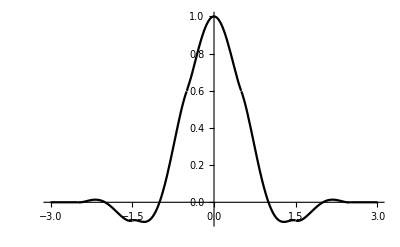

```mathematica
Sol=NSols[[81]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```